```mathematica
<<SpinorHelicity6D`
```

===============SpinorHelicity6D================

Authors: Manuel Accettulli Huber (QMUL)

Please report any bug to:

m.accettullihuber@qmul.ac.uk

Version 1.2 , last update 05/06/2020

=============================================

## SchoutenSimplify

### First basic version, does not work with powers

```mathematica
SchoutenSimplify2[exp_]:=Simplify[exp,TransformationFunctions->{Automatic,e ↦ e/.{SpinorAngleBracket[x_,y_]*SpinorAngleBracket[z_,k_]:>-SpinorAngleBracket[x,z]SpinorAngleBracket[k,y]-SpinorAngleBracket[x,k]SpinorAngleBracket[y,z]},e ↦ e/.{SpinorSquareBracket[x_,y_]*SpinorSquareBracket[z_,k_]:>-SpinorSquareBracket[x,z]SpinorSquareBracket[k,y]-SpinorSquareBracket[x,k]SpinorSquareBracket[y,z]}}]
```

```mathematica
test=14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2;
%//SchoutenSimplify2
%%//SchoutenSimplify
```

14^2 23^2+13^2 24^2+12 13 24 34+12^2 34^2+14 23 (13 24+12 34)

3 13^2 24^2-12 13 24 34+12^2 34^2

#### Try incorporating power rules, some tests which did not work

```mathematica
(*This might be one not very practical way*)
```

```mathematica
SchoutenSimplify2[exp_]:=Simplify[exp,TransformationFunctions->{Automatic,e ↦ e/.{SpinorAngleBracket[x_,y_]*SpinorAngleBracket[z_,k_]:>-SpinorAngleBracket[x,z]SpinorAngleBracket[k,y]-SpinorAngleBracket[x,k]SpinorAngleBracket[y,z]},e ↦ e/.{Power[SpinorAngleBracket[x_,y_],n_?Positive]*Power[SpinorAngleBracket[z_,k_],m_?Positive]/;n≥m:>Power[SpinorAngleBracket[x,y],n-m]Power[-SpinorAngleBracket[x,z]SpinorAngleBracket[k,y]-SpinorAngleBracket[x,k]SpinorAngleBracket[y,z],m]},e ↦ e/.{SpinorSquareBracket[x_,y_]*SpinorSquareBracket[z_,k_]:>-SpinorSquareBracket[x,z]SpinorSquareBracket[k,y]-SpinorSquareBracket[x,k]SpinorSquareBracket[y,z]},e ↦ e/.{Power[SpinorSquareBracket[x_,y_],n_?Positive]*Power[SpinorSquareBracket[z_,k_],m_?Positive]/;n≥m:>Power[SpinorSquareBracket[x,y],n-m]Power[-SpinorSquareBracket[x,z]SpinorSquareBracket[k,y]-SpinorSquareBracket[x,k]SpinorSquareBracket[y,z],m]}},ComplexityFunction->ComplicatedComplexityFunction]
```

```mathematica
test//SchoutenSimplify2
```

14^2 23^2+13^2 24^2+12 13 24 34+12^2 34^2+14 23 (13 24+12 34)

```mathematica
(*The issue here is that if we have A^3*B^2 and we just need a single A*B to simplify through Schouten, the code will never recognise it...*)
```

```mathematica
Attributes[Times]
```

{Flat,Listable,NumericFunction,OneIdentity,Orderless,Protected}

```mathematica
?Flat
```

```mathematica
?OneIdentity
```

```mathematica
?Times
```

```mathematica
a*b/.a^n_.*b^m_.:>{{a,n},{b,m}}
```

{{a,1},{b,1}}

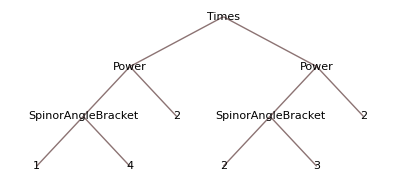

```mathematica
14^2 23^2//TreeForm
```

```mathematica
SchoutenSimplify2[exp_]:=Simplify[exp,TransformationFunctions->{Automatic,e ↦ e/.{SpinorAngleBracket[x_,y_]^n_*SpinorAngleBracket[z_,k_]^m_./;n≥m:>SpinorAngleBracket[x,y]^(n-1)*SpinorAngleBracket[z,k]^(m-1)*(-SpinorAngleBracket[x,z]SpinorAngleBracket[k,y]-SpinorAngleBracket[x,k]SpinorAngleBracket[y,z])}}]
```

```mathematica
test//SchoutenSimplify2
```

14^2 23^2+13^2 24^2+12 13 24 34+12^2 34^2+14 23 (13 24+12 34)

```mathematica
14 23 (13 24+12 34)//SchoutenSimplify2
```

14 23 (13 24+12 34)

```mathematica
(13 24+12 43)//SchoutenSimplify2
```

13 24-12 34

```mathematica
A^2*B^(-3)/.{A^n_.*B^m_.:>A^(n-1)B^(m-1)*C}
```

(A C)/B^4

```mathematica
ComplicatedComplexityFunction[exp_]:=(Print[exp];LeafCount[exp])
```

```mathematica
Simplify[(13 24+12 43),ComplexityFunction->ComplicatedComplexityFunction,TransformationFunctions->{Automatic,e ↦ e/.{SpinorAngleBracket[x_,y_]^n_.*SpinorAngleBracket[z_,k_]^m_.:>SpinorAngleBracket[x,y]^(n-1)*SpinorAngleBracket[z,k]^(m-1)*(-SpinorAngleBracket[x,z]SpinorAngleBracket[k,y]-SpinorAngleBracket[x,k]SpinorAngleBracket[y,z])}}]
```

13 24-12 34

13 24-12 34

13 24-12 34

«4 more identical outputs»

13 24

13 24

13 24

«1 more identical outputs»

13

13

13

«2 more identical outputs»

24

24

24

«2 more identical outputs»

13 24

13 24

13 24

«2 more identical outputs»

-12 34

-12 34

-12 34

«1 more identical outputs»

12

12

12

«2 more identical outputs»

34

34

34

«2 more identical outputs»

-12 34

-12 34

-12 34

«2 more identical outputs»

13 24-12 34

13 24-12 34

13 24-12 34

«2 more identical outputs»

13 24

13 24

13 24

«1 more identical outputs»

13

13

13

«2 more identical outputs»

24

24

24

«2 more identical outputs»

13 24

13 24

13 24

«2 more identical outputs»

-12 34

-12 34

-12 34

«1 more identical outputs»

12

12

12

«2 more identical outputs»

34

34

34

«2 more identical outputs»

-12 34

-12 34

-12 34

«2 more identical outputs»

13 24-12 34

13 24-12 34

13 24-12 34

```mathematica
13 24-12 34/.{Plus->Times,Times->Plus}
```

(13+24) (-1+12+34)

```mathematica
%//Expand
```

-13+12 13-24+12 24+13 34+24 34

#### Another try

```mathematica
SchoutenSimplify2[exp_]:=Simplify[exp,TransformationFunctions->{Automatic,e ↦e/.{SpinorAngleBracket[x_,y_]*SpinorAngleBracket[z_,k_]:>-SpinorAngleBracket[x,z]SpinorAngleBracket[k,y]-SpinorAngleBracket[x,k]SpinorAngleBracket[y,z]}}]
```

### Try completely changing approach

#### A not too good idea

```mathematica
(*I don't think this is a good idea, because Power has a lot of properties and interactions with other functions which I would need to define in order to get proper simplifications*)
```

```mathematica
Attributes[Power]
```

{Listable,NumericFunction,OneIdentity,Protected}

```mathematica
SetAttributes[myPower,Orderless]
```

```mathematica
tomyPower[exp_]:=exp/.{Power[x_,n_]:>myPower[Sequence@@Table[x,{i,n}]]}
```

```mathematica
test=14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2;
```

```mathematica
test//tomyPower
```

myPower[14,14] myPower[23,23]+myPower[13,13] myPower[24,24]+myPower[12,12] myPower[34,34]+13 14 23 24+12 14 23 34+12 13 24 34

#### Something else

```mathematica
test/.Times[f_[SpinorAngleBracket[1,4],___],g_[SpinorAngleBracket[2,3],___],x___]:>Times[A,x]
```

A+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2

```mathematica
a*b/. a_^n_.*b_^m_.:>{{a,n},{b,m}}
```

{{a,1},{b,1}}

```mathematica
PolynomialReduce[test,SpinorAngleBracket[1,4]SpinorAngleBracket[2,3]+SpinorAngleBracket[1,2]SpinorAngleBracket[3,4]+SpinorAngleBracket[1,3]SpinorAngleBracket[4,2],{SpinorAngleBracket[1,2],SpinorAngleBracket[1,3],SpinorAngleBracket[1,4],SpinorAngleBracket[2,3],SpinorAngleBracket[2,4],SpinorAngleBracket[3,4]}]
```

{{2 13 24+12 34},14^2 23^2-13 14 23 24+3 13^2 24^2}

```mathematica
?PolynomialReduce
```

```mathematica
PolynomialReduce[test,SpinorAngleBracket[1,4]SpinorAngleBracket[2,3],{SpinorAngleBracket[1,4],SpinorAngleBracket[2,3]}]
%[[1,1]]*SpinorAngleBracket[1,4]SpinorAngleBracket[2,3]+%[[2]]-test//Simplify
```

{{14 23+13 24+12 34},13^2 24^2+12 13 24 34+12^2 34^2}

0

```mathematica
SchoutenSimplify2[test]
```

14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2

14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2

14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2

«7 more identical outputs»

14^2 23^2

14^2 23^2

14^2 23^2

«4 more identical outputs»

14 23

14 23

14 23

«4 more identical outputs»

14

14

14

«5 more identical outputs»

23

23

23

«5 more identical outputs»

14 23

14 23

14 23

«2 more identical outputs»

14^2

14^2

14^2

«7 more identical outputs»

23^2

23^2

23^2

«7 more identical outputs»

14^2 23^2

14^2 23^2

14^2 23^2

«2 more identical outputs»

13 14 23 24

13 14 23 24

13 14 23 24

«4 more identical outputs»

13

13

13

«5 more identical outputs»

24

24

24

«5 more identical outputs»

13 14 23 24

13 14 23 24

13 14 23 24

«2 more identical outputs»

13^2 24^2

13^2 24^2

13^2 24^2

«4 more identical outputs»

13 24

13 24

13 24

«9 more identical outputs»

13^2

13^2

13^2

«7 more identical outputs»

24^2

24^2

24^2

«7 more identical outputs»

13^2 24^2

13^2 24^2

13^2 24^2

«2 more identical outputs»

12 14 23 34

12 14 23 34

12 14 23 34

«4 more identical outputs»

12

12

12

«5 more identical outputs»

34

34

34

«5 more identical outputs»

12 14 23 34

12 14 23 34

12 14 23 34

«2 more identical outputs»

12 13 24 34

12 13 24 34

12 13 24 34

«9 more identical outputs»

12^2 34^2

12^2 34^2

12^2 34^2

«4 more identical outputs»

12 34

12 34

12 34

«9 more identical outputs»

12^2

12^2

12^2

«7 more identical outputs»

34^2

34^2

34^2

«7 more identical outputs»

12^2 34^2

12^2 34^2

12^2 34^2

«2 more identical outputs»

14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2

14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2

14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2

«2 more identical outputs»

14^2 23^2

14^2 23^2

14^2 23^2

«4 more identical outputs»

14 23

14 23

14 23

«4 more identical outputs»

14

14

14

«5 more identical outputs»

23

23

23

«5 more identical outputs»

14 23

14 23

14 23

«2 more identical outputs»

14^2

14^2

14^2

«7 more identical outputs»

23^2

23^2

23^2

«7 more identical outputs»

14^2 23^2

14^2 23^2

14^2 23^2

«2 more identical outputs»

14 (13 23 24+12 23 34)

14 (13 23 24+12 23 34)

14 (13 23 24+12 23 34)

«3 more identical outputs»

13 14 23 24+12 14 23 34

13 23 24+12 23 34

13 23 24+12 23 34

13 23 24+12 23 34

«4 more identical outputs»

23 (13 24+12 34)

23 (13 24+12 34)

23 (13 24+12 34)

«4 more identical outputs»

13 23 24+12 23 34

13 24+12 34

13 24+12 34

13 24+12 34

«7 more identical outputs»

13 24

13 24

13 24

«4 more identical outputs»

13

13

13

«5 more identical outputs»

24

24

24

«5 more identical outputs»

13 24

13 24

13 24

«2 more identical outputs»

12 34

12 34

12 34

«4 more identical outputs»

12

12

12

«5 more identical outputs»

34

34

34

«5 more identical outputs»

12 34

12 34

12 34

«2 more identical outputs»

13 24+12 34

13 24+12 34

13 24+12 34

«2 more identical outputs»

13 24

13 24

13 24

«4 more identical outputs»

13

13

13

«5 more identical outputs»

24

24

24

«5 more identical outputs»

13 24

13 24

13 24

«2 more identical outputs»

12 34

12 34

12 34

«4 more identical outputs»

12

12

12

«5 more identical outputs»

34

34

34

«5 more identical outputs»

12 34

12 34

12 34

«2 more identical outputs»

13 24+12 34

23 (13 24+12 34)

23 (13 24+12 34)

23 (13 24+12 34)

«1 more identical outputs»

13 23 24+12 23 34

14 23 (13 24+12 34)

14 23 (13 24+12 34)

14 23 (13 24+12 34)

«4 more identical outputs»

13 14 23 24+12 14 23 34

14 23 (13 24+12 34)

14 23 (13 24+12 34)

14 23 (13 24+12 34)

«1 more identical outputs»

13 14 23 24+12 14 23 34

13^2 24^2+12 13 24 34+12^2 34^2

13^2 24^2+12 13 24 34+12^2 34^2

13^2 24^2+12 13 24 34+12^2 34^2

«7 more identical outputs»

13^2 24^2

13^2 24^2

13^2 24^2

«4 more identical outputs»

13^2

13^2

13^2

«7 more identical outputs»

24^2

24^2

24^2

«7 more identical outputs»

13^2 24^2

13^2 24^2

13^2 24^2

«2 more identical outputs»

12 13 24 34

12 13 24 34

12 13 24 34

«9 more identical outputs»

12^2 34^2

12^2 34^2

12^2 34^2

«4 more identical outputs»

12^2

12^2

12^2

«7 more identical outputs»

34^2

34^2

34^2

«7 more identical outputs»

12^2 34^2

12^2 34^2

12^2 34^2

«2 more identical outputs»

13^2 24^2+12 13 24 34+12^2 34^2

13^2 24^2+12 13 24 34+12^2 34^2

13^2 24^2+12 13 24 34+12^2 34^2

«2 more identical outputs»

13^2 24^2

13^2 24^2

13^2 24^2

«4 more identical outputs»

13^2

13^2

13^2

«7 more identical outputs»

24^2

24^2

24^2

«7 more identical outputs»

13^2 24^2

13^2 24^2

13^2 24^2

«2 more identical outputs»

12 13 24 34

12 13 24 34

12 13 24 34

«9 more identical outputs»

12^2 34^2

12^2 34^2

12^2 34^2

«4 more identical outputs»

12^2

12^2

12^2

«7 more identical outputs»

34^2

34^2

34^2

«7 more identical outputs»

12^2 34^2

12^2 34^2

12^2 34^2

«2 more identical outputs»

13^2 24^2+12 13 24 34+12^2 34^2

14^2 23^2+13^2 24^2+12 13 24 34+12^2 34^2+14 23 (13 24+12 34)

14^2 23^2+13^2 24^2+12 13 24 34+12^2 34^2+14 23 (13 24+12 34)

14^2 23^2+13^2 24^2+12 13 24 34+12^2 34^2+14 23 (13 24+12 34)

«3 more identical outputs»

14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2

14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2

14^2 23^2+13^2 24^2+12 13 24 34+12^2 34^2+14 23 (13 24+12 34)

14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2

14^2 23^2+13^2 24^2+12 13 24 34+12^2 34^2+14 23 (13 24+12 34)

14 23 (13 24+12 34)

14 23 (13 24+12 34)

14 23 (13 24+12 34)

«3 more identical outputs»

13 14 23 24+12 14 23 34

13 24+12 34

13 24+12 34

13 24+12 34

«13 more identical outputs»

14 23 (13 24+12 34)

14 23 (13 24+12 34)

14 23 (13 24+12 34)

«1 more identical outputs»

13 14 23 24+12 14 23 34

14^2 23^2+13^2 24^2+12 13 24 34+12^2 34^2+14 23 (13 24+12 34)

14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2

14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2

14^2 23^2+13 14 23 24+13^2 24^2+12 14 23 34+12 13 24 34+12^2 34^2

«1 more identical outputs»

14^2 23^2+13^2 24^2+12 13 24 34+12^2 34^2+14 23 (13 24+12 34)

14^2 23^2+13^2 24^2+12 13 24 34+12^2 34^2+14 23 (13 24+12 34)

14^2 23^2+13^2 24^2+12 13 24 34+12^2 34^2+14 23 (13 24+12 34)